```mathematica
data=Import["/home/stig/from windows/УЧЁБА!!!!!/4 курс/Диплом/coding/1.06.2016/sampleProcess/build-sampleProcess-Desktop-Debug/res_*.csv"];
mean=Import["/home/stig/from windows/УЧЁБА!!!!!/4 курс/Диплом/coding/1.06.2016/sampleProcess/build-sampleProcess-Desktop-Debug/mean.csv"];
xTrajs=Table[{data[[i,j,1]],data[[i,j,2]]},{i,Length@data},{j,Length[data[[i]]]}];
yTrajs=Table[{data[[i,j,1]],data[[i,j,3]]},{i,Length@data},{j,Length[data[[i]]]}];
xMean=Transpose[{mean[[;;,1]],mean[[;;,2]]}];
yMean=Transpose[{mean[[;;,1]],mean[[;;,3]]}];
```

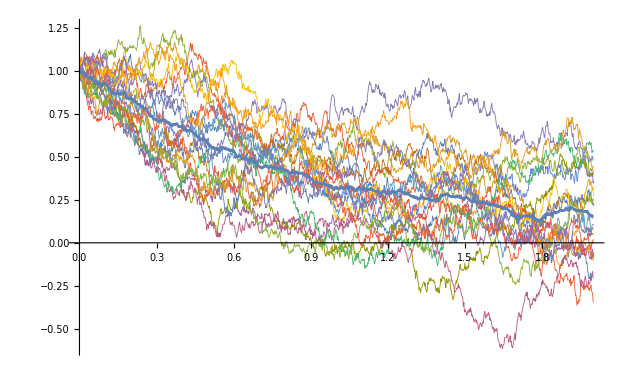
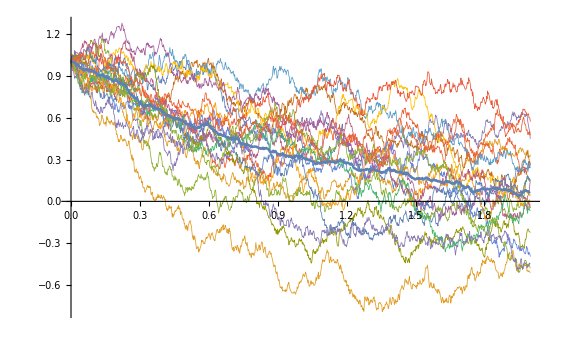

```mathematica
{Show[ListLinePlot[xTrajs,PlotStyle->Thickness[0.001]],ListLinePlot[xMean,PlotStyle->Thickness[0.003]]],Show[ListLinePlot[yTrajs,PlotStyle->Thickness[0.001]],ListLinePlot[yMean,PlotStyle->Thickness[0.003]]]}
```

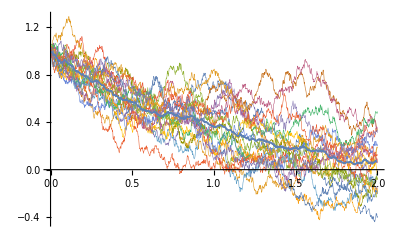
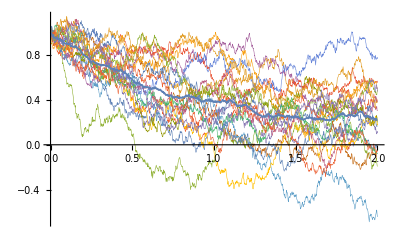

```mathematica
data1=Import["/home/stig/from windows/УЧЁБА!!!!!/4 курс/Диплом/coding/1.06.2016/sampleProcess/build-sampleProcess-Desktop-Debug/res1_*.csv"];
mean1=Import["/home/stig/from windows/УЧЁБА!!!!!/4 курс/Диплом/coding/1.06.2016/sampleProcess/build-sampleProcess-Desktop-Debug/mean1.csv"];
xTrajs1=Table[{data1[[i,j,1]],data1[[i,j,2]]},{i,Length@data1},{j,Length[data1[[i]]]}];
yTrajs1=Table[{data1[[i,j,1]],data1[[i,j,3]]},{i,Length@data1},{j,Length[data1[[i]]]}];
xMean1=Transpose[{mean1[[;;,1]],mean1[[;;,2]]}];
yMean1=Transpose[{mean1[[;;,1]],mean1[[;;,3]]}];
{Show[ListLinePlot[xTrajs1,PlotStyle->Thickness[0.001]],ListLinePlot[xMean1,PlotStyle->Thickness[0.003]]],Show[ListLinePlot[yTrajs1,PlotStyle->Thickness[0.001]],ListLinePlot[yMean1,PlotStyle->Thickness[0.003]]]}
```

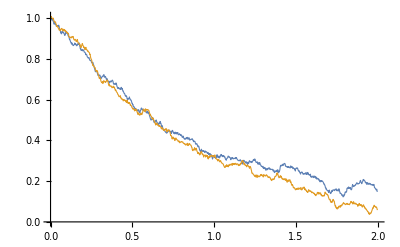

```mathematica
ListLinePlot[{xMean,yMean},PlotStyle->Thickness[0.002]]
```

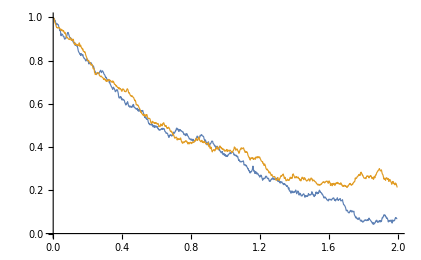

```mathematica
ListLinePlot[{xMean1,yMean1},PlotStyle->Thickness[0.002]]
```

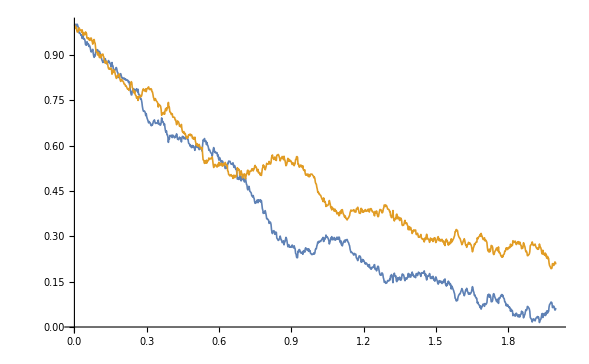

```mathematica
mean2=Import["/home/stig/from windows/УЧЁБА!!!!!/4 курс/Диплом/coding/1.06.2016/sampleProcess/build-sampleProcess-Desktop-Debug/mean2.csv"];
xMean2=Transpose[{mean2[[;;,1]],mean2[[;;,2]]}];
yMean2=Transpose[{mean2[[;;,1]],mean2[[;;,3]]}];
ListLinePlot[{xMean2,yMean2},PlotStyle->Thickness[0.002]]
```